# Metodi Monte Carlo a catena di Markov : algoritmo di Metropolis per il TSP (variante senza obbligo di ritorno alla stessa città di partenza): diversi valori di beta

Vettore di stato iniziale: Luxembourg, Zurich, Gothenburg, Edinburgh, Marseille, Prague, Sofia, Munich, Belgrade, Naples, Tirana, Riga, Oslo, London, Moscow, Vilnius, Bucharest, Porto, Bratislava, Helsinki

Percorso Minimo:

Luxembourg, Zurich, Marseille, Porto, London, Edinburgh, Gothenburg, Oslo, Riga, Helsinki, Moscow, Vilnius, Bucharest, Sofia, Tirana, Belgrade, Bratislava, Prague, Munich, Naples

Percentuali di accettazione, per ogni beta: {99.,60.5,22.,14.5}

Minimi trovati, per ogni beta: {21958.5,16854.8,15856.4,11985.}

Variazione media di distanza per le scelte accettate, per ogni beta: {18.0449,4.85974,-266.261,-732.879}

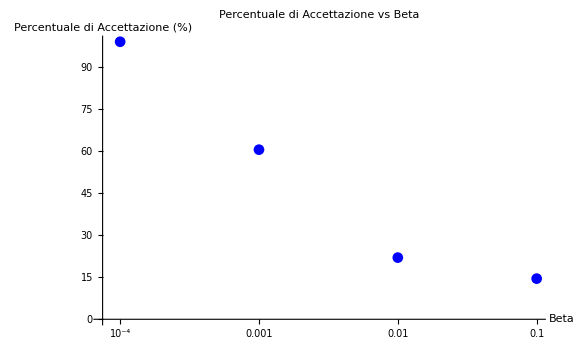

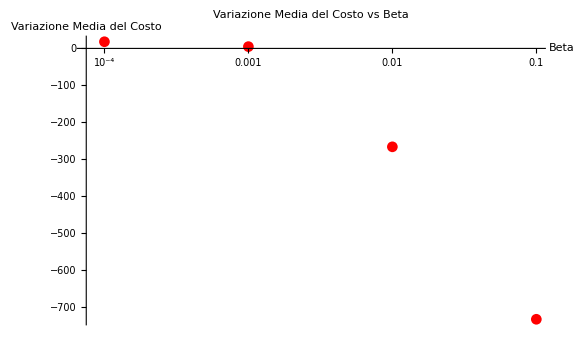

-Graphics-

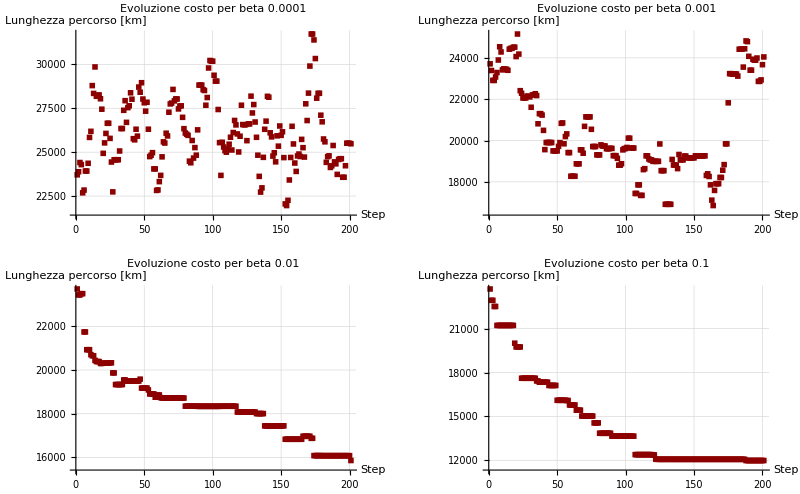

Variazione media di distanza per le scelte accettate, per ogni beta: {-33.7324,-43.8992,-120.54,-113.843}

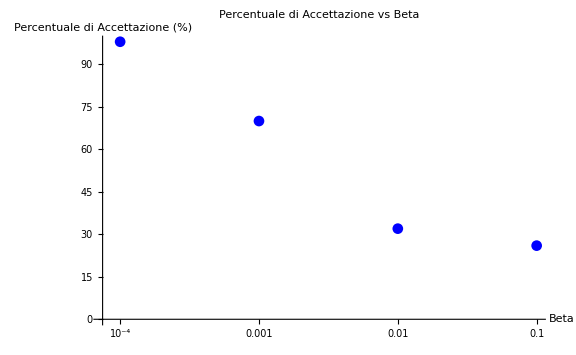

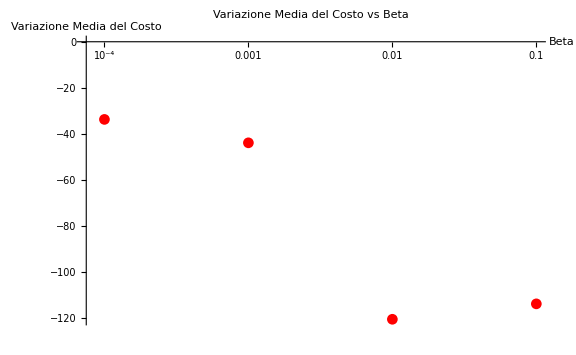

-Graphics-

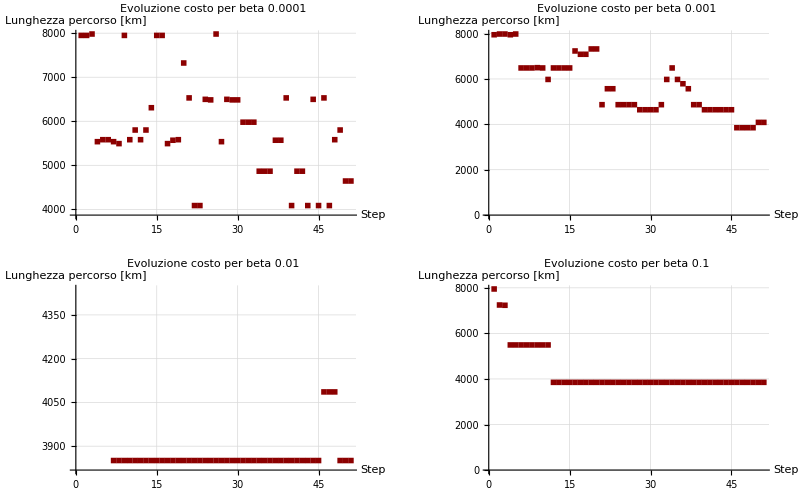

```mathematica
(*L'obiettivo è cercare mediante l'algoritmo di Metropolis un minimo della funzione costo per il TSP,per DIVERSI VALORI DI BETA.*)n=20; (*numero di città*)

(*Dati delle città*)
città={<|"nome"->"Amsterdam","lat"->52.3676,"long"->4.9041|>,<|"nome"->"Athens","lat"->37.9838,"long"->23.7275|>,<|"nome"->"Barcelona","lat"->41.3851,"long"->2.1734|>,<|"nome"->"Belgrade","lat"->44.7866,"long"->20.4489|>,<|"nome"->"Berlin","lat"->52.5200,"long"->13.4050|>,<|"nome"->"Bern","lat"->46.9481,"long"->7.4474|>,<|"nome"->"Bratislava","lat"->48.1486,"long"->17.1077|>,<|"nome"->"Brussels","lat"->50.8503,"long"->4.3517|>,<|"nome"->"Bucharest","lat"->44.4268,"long"->26.1025|>,<|"nome"->"Budapest","lat"->47.4979,"long"->19.0402|>,<|"nome"->"Copenhagen","lat"->55.6761,"long"->12.5683|>,<|"nome"->"Dublin","lat"->53.3498,"long"->-6.2603|>,<|"nome"->"Edinburgh","lat"->55.9533,"long"->-3.1883|>,<|"nome"->"Frankfurt","lat"->50.1109,"long"->8.6821|>,<|"nome"->"Geneva","lat"->46.2044,"long"->6.1432|>,<|"nome"->"Helsinki","lat"->60.1695,"long"->24.9354|>,<|"nome"->"Istanbul","lat"->41.0082,"long"->28.9784|>,<|"nome"->"Kiev","lat"->50.4501,"long"->30.5234|>,<|"nome"->"Lisbon","lat"->38.7223,"long"->-9.1393|>,<|"nome"->"Ljubljana","lat"->46.0569,"long"->14.5058|>,<|"nome"->"London","lat"->51.5074,"long"->-0.1278|>,<|"nome"->"Luxembourg","lat"->49.6116,"long"->6.1319|>,<|"nome"->"Madrid","lat"->40.4168,"long"->-3.7038|>,<|"nome"->"Milan","lat"->45.4642,"long"->9.1900|>,<|"nome"->"Monaco","lat"->43.7384,"long"->7.4246|>,<|"nome"->"Moscow","lat"->55.7558,"long"->37.6173|>,<|"nome"->"Munich","lat"->48.1351,"long"->11.5820|>,<|"nome"->"Oslo","lat"->59.9139,"long"->10.7522|>,<|"nome"->"Paris","lat"->48.8566,"long"->2.3522|>,<|"nome"->"Prague","lat"->50.0755,"long"->14.4378|>,<|"nome"->"Reykjavik","lat"->64.1355,"long"->-21.8954|>,<|"nome"->"Riga","lat"->56.9496,"long"->24.1052|>,<|"nome"->"Sarajevo","lat"->43.8563,"long"->18.4131|>,<|"nome"->"Sofia","lat"->42.6977,"long"->23.3219|>,<|"nome"->"Stockholm","lat"->59.3293,"long"->18.0686|>,<|"nome"->"Tallinn","lat"->59.4370,"long"->24.7535|>,<|"nome"->"Tirana","lat"->41.3275,"long"->19.8189|>,<|"nome"->"Valletta","lat"->35.8989,"long"->14.5146|>,<|"nome"->"Vienna","lat"->48.2082,"long"->16.3738|>,<|"nome"->"Vilnius","lat"->54.6872,"long"->25.2797|>,<|"nome"->"Warsaw","lat"->52.2297,"long"->21.0122|>,<|"nome"->"Zagreb","lat"->45.8150,"long"->15.9819|>,<|"nome"->"Zurich","lat"->47.3769,"long"->8.5417|>,<|"nome"->"Seville","lat"->37.3891,"long"->-5.9845|>,<|"nome"->"Naples","lat"->40.8522,"long"->14.2681|>,<|"nome"->"Lyon","lat"->45.7640,"long"->4.8357|>,<|"nome"->"Porto","lat"->41.1579,"long"->-8.6291|>,<|"nome"->"Gothenburg","lat"->57.7089,"long"->11.9746|>,<|"nome"->"Marseille","lat"->43.2965,"long"->5.3698|>,<|"nome"->"Cologne","lat"->50.9375,"long"->6.9603|>};

(*Funzione per creare lo stato iniziale con n città*)
creaStato[città_,n_]:=Module[{scelte},scelte=RandomSample[città,n];
Join[{First[scelte]},Rest[scelte]]]

(*Funzione per calcolare la distanza tra due città*)
distanza[città1_,città2_]:=QuantityMagnitude[GeoDistance[{città1[["lat"]],città1[["long"]]},{città2[["lat"]],città2[["long"]]}]]

(*Funzione per calcolare la distanza totale di un percorso*)
distanzatot[stato_]:=Total[Table[distanza[stato[[i]],stato[[i+1]]],{i,1,Length[stato]-1}]]

(*Funzione per stampare il percorso*)
stampa[stato_]:=StringJoin[Riffle[stato[[All,"nome"]],", "]]


(*Funzione per creare un nuovo stato *)
creaNuovoStato[stato_]:=Module[{rand1,rand2,minRand,maxRand,invertito},{rand1,rand2}=RandomInteger[{2,n},2];
{minRand,maxRand}=Sort[{rand1,rand2}];
invertito=Reverse[stato[[minRand;;maxRand]]];
Join[stato[[1;;minRand-1]],invertito,stato[[maxRand+1;;n]]]];

stampaNomiPercorsoMinimo[percorsoMinimo_]:=Module[{nomiCittà},(*Estrai i nomi delle città dal percorso minimo*)nomiCittà=percorsoMinimo[[All,"nome"]];
(*Stampa i nomi delle città come una stringa separata da virgole*)Print[StringJoin[Riffle[nomiCittà,", "]]]]

(*Parametri per l'algoritmo di Metropolis*)
rip=10*n; (*numero di ripetizioni per ciascun valore di beta*) 

numBeta=4; (*numero di beta*)
vettBeta={0.0001,0.001,0.01,0.1}; (*vettore dei beta: innalzamento di beta, cioè abbassamento della temperatura*)
numAccettazioni=Table[0,numBeta]; (*vettore contentente in numero di accettazioni per ogni beta*)
minimi=Table[0,numBeta]; (*vettore dei percorsi che minimizzano il costo per ogni beta*)
storia=Table[Table[0,rip +1],numBeta]; (*successione delle distanze accettate per ogni beta*)
varCostoMedio= Table[0, numBeta];
(*per ogni beta sommo le variazioni di distanza per gli stati accettati; dividerò poi per il numero di MCSS per ottenere il deltacostomedio*)
memorizzaPercorsi=Table[{},numBeta];

(*Creazione dello stato iniziale*)
statoIniz=creaStato[città,n];
Print["Vettore di stato iniziale: ", stampa[statoIniz]];


(*Algoritmo di Metropolis*)
For[j=1,j<=numBeta,j++,stato=statoIniz;(*parto sempre dallo stesso stato iniziale!*)
minimi[[j]]=distanzatot[stato];
storia[[j,1]]=distanzatot[stato];
For[i=1,i<=rip,i++,nuovostato=creaNuovoStato[stato];
varCosto=distanzatot[nuovostato]-distanzatot[stato];
If[varCosto<0||Exp[-vettBeta[[j]]*varCosto]>RandomReal[],stato=nuovostato;
numAccettazioni[[j]]++;
varCostoMedio[[j]]+=varCosto;
If[distanzatot[stato]<minimi[[j]],
minimi[[j]]=distanzatot[stato];
memorizzaPercorsi[[j]]=stato;
];
];  
storia[[j,i+1]]=distanzatot[stato];
];
]



(*Calcolo variazione costo medio delle scelte accettate per ogni beta*)
For[t=1, t<=numBeta, t++,
varCostoMedio[[t]]=N[varCostoMedio[[t]]/percAccettazione[[t]]]
];

(*Calcolo della percentuale di accettazione*)
percAccettazione=N[100*(numAccettazioni/rip),3];

numMinBeta=Position[minimi,Min[minimi]];
(*numMinBeta potrebbe essere una lista di indici,e potremmo aver bisogno di prendere il primo elemento*)
numMinBetaIndice=numMinBeta[[1,1]];
percorsoMinimo=memorizzaPercorsi[[numMinBetaIndice]];

(*Supponiamo che memorizzaPercorsi e minimi siano corretti*)numMinBeta=Position[minimi,Min[minimi]];

(*Assicurati di estrarre l'indice corretto*)
numMinBetaIndice=numMinBeta[[1,1]];

(*Ottieni il percorso minimo*)
percorsoMinimo=memorizzaPercorsi[[numMinBetaIndice]];

(*Stampa il percorso minimo*)
Print["Percorso Minimo:"];
stampaNomiPercorsoMinimo[percorsoMinimo];

(*Estrai le coordinate*)
coordinateCittàMin=Table[{percorsoMinimo[[i,"lat"]],percorsoMinimo[[i,"long"]]},{i,1,Length[percorsoMinimo]}];

(*(*Visualizza le coordinate*)
coordinateCittàMin
*)

(*Risultati*)
Print["Percentuali di accettazione, per ogni beta: ",percAccettazione];
Print["Minimi trovati, per ogni beta: ",minimi];
Print["Variazione media di distanza per le scelte accettate, per ogni beta: ", varCostoMedio]

(*Grafici*)
(*Grafico che rappresenta l'andamento delle percentuali di accettazione in funzione di beta*)

ListLogLinearPlot[Transpose[{vettBeta,percAccettazione}],
PlotRange->All;
PlotMarkers->Automatic,PlotStyle->Blue,AxesLabel->{"Beta","Percentuale di Accettazione (%)"},PlotLabel->"Percentuale di Accettazione vs Beta",GridLines->Automatic,ImageSize->Large]

(*Grafico che rappresenta l'andamento della varaiazione media del costo in funzione di beta*)

ListLogLinearPlot[Transpose[{vettBeta,varCostoMedio}],
PlotRange->All;
PlotMarkers->Automatic,PlotStyle->Red,AxesLabel->{"Beta","Variazione Media del Costo"},PlotLabel->"Variazione Media del Costo vs Beta",GridLines->Automatic,ImageSize->Large]


(*Utilizzare GeoGraphics per plottare il percorso minimo sulla mappa*)

GeoGraphics[{(*Disegnare il percorso in blu spesso*){Blue,Thickness[0.01],GeoPath[coordinateCittàMin,"Geodesic"]},(*Aggiungere marcatori rossi per ogni città*){Red,PointSize[Large],GeoMarker/@coordinateCittàMin}},GeoRange->Automatic,(*Visualizza la mappa del mondo*)GeoBackground->"StreetMap" (*Aggiunge uno sfondo fisico alla mappa*)]

 

(*Lista di grafici per ogni valore di beta*)grafici=Table[ListPlot[storia[[i]],PlotMarkers->{■,0.001},PlotStyle->{RGBColor[0.55,0,0]},AxesLabel->{"Step","Lunghezza percorso [km]"},PlotLabel->"Evoluzione costo per beta "<>ToString[vettBeta[[i]]],GridLines->Automatic,Mesh->All,MeshStyle->{Red}],{i,1,numBeta}];

(*Mostra i grafici in una griglia*)
GraphicsGrid[Partition[grafici,2]]
```